# Лабораторная работа №8

# Интерактивное исследование форматов данных

```mathematica
Wolfram|Alpha Query
```

```mathematica
1. Базовый рабочий процесс
```

```mathematica
ПРИМЕР 1
```

```mathematica
(*WolframAlpha["запрос", формат] - отправляет запрос в Wolfram|Alpha и возвращает результат в заданном формате
При использовании формата "Input" дает левую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "Output" дает правую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "FormulaData" дает полное уравнение в стандартном синтаксисе языка Wolfram Language
HoldComplete[expr] - полностью защищает expr от стандартного процесса оценки Wolfram Language
Hold[expr] - поддерживает expr в неоцененной форме
HoldComplete используется,когда нужно предотвратить определенные этапы процесса оценки,чему Hold не мешает.*)
```

```mathematica
WolframAlpha["integrate cos(3x+2) from -pi/2 to 3pi/2",{{"Input",1},"Input"}]
WolframAlpha["integrate cos(3x+2) from -pi/2 to pi/2",{{"Input",1},"Output"}]
WolframAlpha["integrate cos(3x+2) from 0 to 2pi",{{"Input",1},"FormulaData"}]
```

HoldComplete[∫_(-π/2)^((3 π)/2) Cos[2+3 x]ⅆx]

HoldComplete[-(2 Cos[2])/3]

Hold[∫_0^(2 π) Cos[3 x+2]ⅆx==0]

```mathematica
ПРИМЕР 2
```

```mathematica
(*ReleaseHold[expr] - удаляет один слой Hold,HoldForm,HoldPattern и HoldComplete (все стандартные неоцененные контейнеры) в выражении expr.
% - дает последний полученный результат*)
```

Hold[∫_0^(3 π) Cos[2 x^2-5]ⅆx≈-0.295581]

HoldComplete[Plot[Cos[5-2 x^2],{x,0,3 π}]]

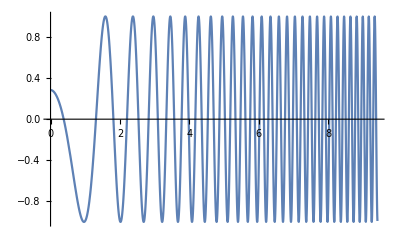

```mathematica
WolframAlpha["integrate cos(2x^2-5) from 0 to 3pi",{{"Input",1},"FormulaData"}]
WolframAlpha["integrate cos(2x^2-5) from 0 to 3pi",{{"VisualRepresentationOfTheIntegral",1},"Input"}]
ReleaseHold[%]
```

```mathematica
2. Открытые форматы данных не обязательно похожи на графический результат
```

```mathematica
(*Запрос ниже должен вычислять акции facebook от 4 марта 2018 года до 25 сентября 2018 года, в 1 столбце дата трасформированная Wolfram|Alpha, во втором цена 1 акции facebook. Если данные за заданный период отсутствуют, то результатом будет Missing["NotAvailable"]*)
(*запустить для output*)
```

```mathematica
WolframAlpha["facebook close March 4, 2018 to March 25 2018",{{"DateRangeSpecified:Close:FinancialData",1},"FormattedData"}]
```

Date | In multiples of 1.00 $
Mon 5 Mar 2018 00:00:00GMT+3. | 180.4
Tue 6 Mar 2018 00:00:00GMT+3. | 179.78
Wed 7 Mar 2018 00:00:00GMT+3. | 183.71
Thu 8 Mar 2018 00:00:00GMT+3. | 182.34
Fri 9 Mar 2018 00:00:00GMT+3. | 185.23
Mon 12 Mar 2018 00:00:00GMT+3. | 184.76
Tue 13 Mar 2018 00:00:00GMT+3. | 181.88
Wed 14 Mar 2018 00:00:00GMT+3. | 184.19
Thu 15 Mar 2018 00:00:00GMT+3. | 183.86
Fri 16 Mar 2018 00:00:00GMT+3. | 185.09
Mon 19 Mar 2018 00:00:00GMT+3. | 172.56
Tue 20 Mar 2018 00:00:00GMT+3. | 168.15
Wed 21 Mar 2018 00:00:00GMT+3. | 169.39
Thu 22 Mar 2018 00:00:00GMT+3. | 164.89
Fri 23 Mar 2018 00:00:00GMT+3. | 159.39

```mathematica
3. Структура второго аргумента
```

```mathematica
(*WolframAlpha[{"podid","subpodid"}, "property"]
podid - строка, созданная Wolfram|Alpha для идентификации модуля
subpodid - представляет собой целое число,указывающее положение конкретного результата в модуле
property - напрямую запрашивает доступные форматы данных для podid*)
```

```mathematica
{WolframAlpha["plot cos(2x^2+5)",{{"Plot",1},"Input"}],WolframAlpha["plot cos(2x^2+5)",{{"Plot",2},"Input"}]}
```

{HoldComplete[Plot[Cos[5-2 x^2],{x,-2.5,2.5}]],HoldComplete[Plot[Cos[5+2 x^2],{x,-3.8,3.8}]]}

```mathematica
Свободная форма ввода
```

```mathematica
(*Например, чтобы получить доступ к вычислимым данным для интеграла из Примера 1 в задании 1,достаточно щёлкнуть по нему правой кнопкой мыши и выбрать Copy As -> Input data*)(*Такой же результат можно извлечь при помощи обращения к свойству ComputableData*)
WolframAlpha["integrate cos(3x+2) from -pi/2 to 3pi/2",{{"Input",1},"ComputableData"}]
```

Hold[∫_(-π/2)^((3 π)/2) Cos[3 x+2]ⅆx==0]

```mathematica
(*И действительно мы получили вычислимые данные*)
```

# Получение форматов данных программными методами

```mathematica
1. Форматы данных как свойства субмодуля
```

```mathematica
(*Имена программных свойств для различных форматов представляют собой строки,полученные из соответствующих имён меню путем объединения слов в одно целое: Computable data становится "ComputableData",Time series data становится "TimeSeriesData",Input становится "Input".*)
```

```mathematica
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"DateRangeSpecified:Close:FinancialData",1},"TimeSeriesData"}]
```

{{{2020,4,27,0,0,0.},187.50 $},{{2020,4,28,0,0,0.},182.91 $},{{2020,4,29,0,0,0.},194.19 $},{{2020,4,30,0,0,0.},204.71 $}}

```mathematica
2. Определение доступных форматов
```

```mathematica
(*Форматы данных,доступные для конкретного субмодуля,содержатся в свойстве «DataFormats» каждого субмодуля.Это свойство можно вычислить так же,как и любое другое свойство вложенного модуля.*)
```

```mathematica
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{All,"DataFormats"}]
```

{{{Input,1},DataFormats}→{Plaintext,Input,ComputableData,FormattedData},{{Result,1},DataFormats}→{Plaintext,ComputableData,FormattedData,NumberData,QuantityData},{{DateRangeSpecified:Close:FinancialData,1},DataFormats}→{ComputableData,FormattedData,TimeSeriesData}}

```mathematica
3. Прямые запросы данных
```

```mathematica
(*В WolframAlpha["podid","property"]
podid - строка, созданная Wolfram|Alpha для идентификации модуля
property - напрямую запрашивает доступные форматы данных для podid*)
```

```mathematica
WolframAlpha["5*3+2","PodIDs"]
```

{Input,Result,NumberLine,NumberName,VisualRepresentation,PercentIncrease/decrease}

```mathematica
WolframAlpha["5*3+2",{All,{"Output","FormulaData"}}]
```

{{{Result,1},Output}→HoldComplete[17],{{PercentIncrease/decrease,1},Output}→HoldComplete[13.3333],{{Input,1},FormulaData}→Hold[5 3+2],{{Result,1},FormulaData}→Hold[17]}

```mathematica
(*Можно запрашивать определенные форматы из определенного подмодуля.В случае,если конкретный формат недоступен,мы все равно получаем правило для него с правой частью Missing["NotAvailable"]:*)
```

```mathematica
WolframAlpha["5*3+2",{{"Result",1},{"Output","FormulaData"}}]
```

{{{Result,1},Output}→HoldComplete[17],{{Result,1},FormulaData}→Hold[17]}

# Примеры открытых данных

```mathematica
1. Величины и числа
```

```mathematica
(*  Показывает все данные об акциях и их измерениях в виде таблицы, в промежутке с 27 по 30 апреля 2020 года в виде списка *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"Result",1},"FormattedData"}]
(*  Показывает все данные об акциях и их измерениях в виде списка, в промежутке с 27 по 30 апреля 2020 года в виде списка *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"Result",1},"ComputableData"}]
(*  Показывает все данные об акциях в виде списка чисел, в промежутке с 27 по 30 апреля 2020 года в виде списка *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"Result",1},"NumberData"}]
(*  Показывает данные об акциях в виде списка, в промежутке с 27 по 30 апреля 2020 года в виде списка *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"Result",1},"QuantityData"}]
```

mean | 192.33 $
highest | 204.71 $
lowest | 182.91 $
change | 9.2 %

{{mean,192.33 $},{highest,204.71 $},{lowest,182.91 $},{change,9.2 %}}

{192.33,204.71,182.91,9.2}

{192.33 $,204.71 $,182.91 $,9.2 %}

```mathematica
2. Временные ряды
```

```mathematica
(* Показывает график данных о акциях facebook и дате с 27 по 30 апреля 2020 года в графическом виде *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",IncludePods->"DateRangeSpecified:Close:FinancialData"]
(* Показывает данные facebook в виде вычисляемых данных *)
WolframAlpha["facebook close from Apr 27 to Apr 30, 2020",{{"DateRangeSpecified:Close:FinancialData",1},"ComputableData"}]
```

WolframAlphaQueryResults

{{{2020,4,27,0,0,0.},187.50 $},{{2020,4,28,0,0,0.},182.91 $},{{2020,4,29,0,0,0.},194.19 $},{{2020,4,30,0,0,0.},204.71 $}}

```mathematica
4. Формулы
```

```mathematica
(* Рассмотрим уравнение силы гравитационного притяжения между телами*)
WolframAlpha["force of gravity",{{"Equation",1},"FormattedData"}]
```

Hold[F==(G m_1 m_2)/r^2] | 
Hold[F] | gravitational force
Hold[m_1] | primary mass
Hold[m_2] | secondary mass
Hold[r] | distance
Hold[G] | Newtonian gravitational constant

```mathematica
5. Звуки
```

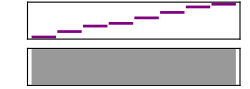

WolframAlphaQueryResults

```mathematica
(*При помощи WolframAlpha находим ноты в ре мажоре и строим их в пределах 1-2 октавы в секвенсере*)
WolframAlpha["d-major scale",{{"MusicNotation",1},"SoundData"}]
(*При помощи WolframAlpha находим ноты в си миноре и строим их в пределах 1-2 октавы в нотная тетради*)
WolframAlpha["b-minor scale",IncludePods->"MusicNotation"]
```